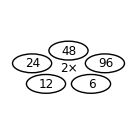

```mathematica
dtn[L_]:=Fold[10#1+#2&,0,L]
```

```mathematica
rem[L_]:=Module[{i},
LL=L;
For[i=2,i<Length[LL],i++,If[LL[[i-1]]<LL[[i]]<LL[[i+1]],LL=Drop[LL,{i}]]];LL]
```

```mathematica
f[n_,k_]:=Module[{A,top,num,flag,id,poss,sol},
sol={};
A={{k}};
flag=True;
While[flag||Length[First[A]]=!=Length[Last[A]],
top=First[A];
A=Rest[A];
num=First[top];
If[num==n,AppendTo[sol,rem[top]];flag=False,
id=IntegerDigits[num];
poss=Join[{2num},Table[dtn[Drop[id,{i}]],{i,1,Length[id]}]];
A=Join[A,Map[Prepend[top,#]&,poss]]]];
sol=Union[sol];If[Length[sol]==1,Print[n," -> ",k,": ",sol[[1]]]]]
```

```mathematica
For[t=3,t≤100,t++,
For[z=1,z≤t-1,z++,If[2z=!=t,f[z,t-z]]]]
```

1 -> 2: {1,16,8,4,2}

1 -> 3: {1,12,6,3}

3 -> 1: {3,32,16,8,4,2,1}

1 -> 4: {1,16,8,4}

2 -> 3: {2,12,6,3}

3 -> 2: {3,32,16,8,4,2}

3 -> 4: {3,32,16,8,4}

6 -> 1: {6,16,8,4,2,1}

6 -> 2: {6,16,8,4,2}

7 -> 1: {7,72,36,18,128,64,32,16,8,4,2,1}

7 -> 2: {7,72,36,18,128,64,32,16,8,4,2}

8 -> 1: {8,4,2,1}

6 -> 4: {6,16,8,4}

9 -> 1: {9,96,48,24,12,6,16,8,4,2,1}

2 -> 9: {2,1,18,9}

3 -> 8: {3,32,16,8}

7 -> 4: {7,72,36,18,128,64,32,16,8,4}

9 -> 2: {9,96,48,24,12,6,16,8,4,2}

3 -> 9: {3,36,18,9}

5 -> 7: {5,56,28,14,7}

9 -> 3: {9,96,48,24,12,6,3}

4 -> 9: {4,2,1,18,9}

6 -> 7: {6,56,28,14,7}

9 -> 4: {9,96,48,24,12,6,16,8,4}

12 -> 1: {12,6,16,8,4,2,1}

12 -> 2: {12,6,16,8,4,2}

6 -> 9: {6,36,18,9}

7 -> 8: {7,72,36,18,128,64,32,16,8}

9 -> 6: {9,96,48,24,12,6}

5 -> 11: {5,352,176,88,44,22,11}

7 -> 9: {7,72,36,18,9}

12 -> 4: {12,6,16,8,4}

9 -> 8: {9,96,48,24,12,6,16,8}

10 -> 7: {10,5,56,28,14,7}

14 -> 3: {14,184,92,192,96,48,24,12,6,3}

16 -> 1: {16,8,4,2,1}

5 -> 13: {5,52,26,13}

6 -> 12: {6,96,48,24,12}

7 -> 11: {7,176,88,44,22,11}

11 -> 7: {11,112,56,28,14,7}

$Aborted

```mathematica
g[n_]:=Module[{A,top,num,flag,id,poss,sol},
sol={};
A={{n}};
flag=True;
While[flag||Length[First[A]]=!=Length[Last[A]],
top=First[A];
A=Rest[A];
num=First[top];
If[num==n&&Length[top]>1,AppendTo[sol,rem[top]];flag=False,
id=IntegerDigits[num];
poss=Join[{7num},Table[dtn[Drop[id,{i}]],{i,1,Length[id]}]];
A=Join[A,Map[Prepend[top,#]&,poss]]]];
sol=Union[sol];If[Length[sol]==1,Print[sol[[1]]]]]
```

```mathematica
For[t=1,t≤2008,t++,g[t]]
```

{2,28,4,14,2}

{4,14,2,28,4}

{5,35,5}

{8,28,4,42,6,56,8}

{12,812,116,4116,588,84,12}

{14,2,28,4,14}

{15,105,15}

{17,40817,5831,833,119,17}

{18,182,26,126,18}

{20,280,40,140,20}

{24,294,42,6,168,24}

{26,126,18,182,26}

{27,6027,861,123,1323,189,27}

{28,4,14,2,28}

{35,5,35}

{36,364,52,252,36}

{37,9037,1291,12691,1813,259,37}

{39,329,47,147,21,3,39}

{40,140,20,280,40}

{41,441,63,9,2009,287,41}

{43,343,49,7,1,301,43}

{47,147,21,3,329,47}

{48,10248,1464,16464,2352,336,48}

{50,350,50}

{52,252,36,364,52}

{54,546,78,378,54}

{55,595,85,385,55}

{77,3773,539,77}

{78,378,54,546,78}

{80,280,40,420,60,560,80}

{83,20083,2869,28469,4067,581,83}

{85,385,55,595,85}

{86,686,98,14,2,602,86}

{87,3087,441,63,9,609,87}

{88,2884,412,4312,616,88}

{96,196,28,4,42,6,96}

$Aborted

```mathematica
For[t=1,t≤2008,t++,If[Mod[t,10]=!=5,g[t]]]
```

{2,12,2}

{3,36,6,1,18,3}

{4,24,4}

{6,36,6}

{7,72,12,2,42,7}

{8,48,8}

{11,1416,236,2376,396,66,11}

{12,2,12}

{13,132,22,252,42,7,78,13}

{14,144,24,4,14}

{16,216,36,6,16}

{17,2172,362,3672,612,102,17}

{18,108,18}

{20,120,20}

{21,216,36,6,1,21}

{24,4,24}

{26,216,36,6,26}

$Aborted

```mathematica
For[t=1,t≤2008,t++,g[t]]
```

{1,81,27,9,3,1}

{2,24,8,18,6,2}

{3,1,81,27,9,3}

{5,15,5}

{8,18,6,2,24,8}

{9,3,1,81,27,9}

{10,810,270,90,30,10}

{11,171,57,19,8019,2673,891,297,99,33,11}

{15,5,15}

{16,162,54,18,6,16}

{20,240,80,180,60,20}

{22,282,94,594,198,66,22}

{24,8,18,6,2,24}

{25,225,75,25}

{27,9,3,1,81,27}

{30,10,810,270,90,30}

{31,231,77,747,249,83,837,279,93,31}

{33,11,171,57,19,8019,2673,891,297,99,33}

{35,315,105,35}

$Aborted

```mathematica
For[t=1,t≤2008,t++,g[t]]
```

{1,16,8,4,2,1}

{6,96,48,24,12,6}

{9,96,48,24,12,6,36,18,9}

{10,160,80,40,20,10}

{18,128,64,32,16,8,18}

{22,272,136,68,34,17,176,88,44,22}

{25,256,128,64,32,16,8,4,2,25}

{26,256,128,64,32,16,8,4,2,26}

{28,128,64,32,16,8,28}

{36,18,9,96,48,24,12,6,36}

{46,146,73,736,368,184,92,46}

```mathematica
c[n_,k_,num_]:={r=RandomInteger[{1,n}];Table[Circle[{1.15 Csc[Pi/n]Cos[2Pi i/n-Pi/2-Pi/n],1.15 Csc[Pi/n]Sin[2Pi i/n-Pi/2-Pi/n]},1],{i,1,n}],Text[Style[ToString[k]<>"×",FontSize->20],{0,0}],Text[Style[num,FontSize->18],{1.15 Csc[Pi/n]Cos[2Pi r/n-Pi/2-Pi/n]+.03,1.15 Csc[Pi/n]Sin[2Pi r/n-Pi/2-Pi/n]-.05}]}
```

```mathematica
d[n_,k_,L_]:={Table[Circle[{1.15 Csc[Pi/n]Cos[2Pi i/n-Pi/2-Pi/n],1.15 Csc[Pi/n]Sin[2Pi i/n-Pi/2-Pi/n]},1],{i,1,n}],Text[Style[ToString[k]<>"×",FontSize->20],{0,0}],Table[If[Length[IntegerDigits[L[[i]]]]==4,Text[Style[L[[i]],FontSize->14],{1.15 Csc[Pi/n]Cos[2Pi i/n-Pi/2-Pi/n]+.03,1.15 Csc[Pi/n]Sin[2Pi i/n-Pi/2-Pi/n]-.05}],If[Length[IntegerDigits[L[[i]]]]==5,Text[Style[L[[i]],FontSize->11],{1.15 Csc[Pi/n]Cos[2Pi i/n-Pi/2-Pi/n]+.03,1.15 Csc[Pi/n]Sin[2Pi i/n-Pi/2-Pi/n]-.05}],Text[Style[L[[i]],FontSize->18],{1.15 Csc[Pi/n]Cos[2Pi i/n-Pi/2-Pi/n]+.03,1.15 Csc[Pi/n]Sin[2Pi i/n-Pi/2-Pi/n]-.05}]]],{i,1,n}]}
```

```mathematica
dd[n_,k_,L_]:={Table[Circle[{1.15 Csc[Pi/n]Cos[2Pi i/n-Pi/2-Pi/n],1.15 Csc[Pi/n]Sin[2Pi i/n-Pi/2-Pi/n]},1],{i,1,n}],Text[Style[ToString[k]<>"×",FontSize->20],{0,0}],Table[Text[Style[L[[i]],FontSize->14],{1.15 Csc[Pi/n]Cos[2Pi i/n-Pi/2-Pi/n]+.03,1.15 Csc[Pi/n]Sin[2Pi i/n-Pi/2-Pi/n]-.05}],{i,1,n}]}
```

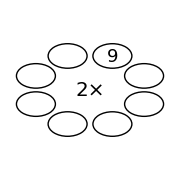

```mathematica
Graphics[c[8,2,9],PlotRange->{-6,6},ImageSize->{180,180}]
```

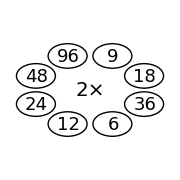

```mathematica
Graphics[d[8,2,{6,36,18,9,96,48,24,12}],PlotRange->{-6,6},ImageSize->{180,180}]
```

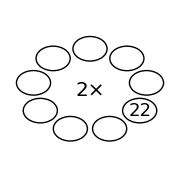

```mathematica
Graphics[c[9,2,22],PlotRange->{-6,6},ImageSize->{180,180}]
```

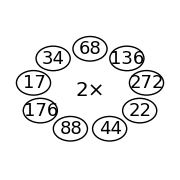

```mathematica
Graphics[d[9,2,{44,22,272,136,68,34,17,176,88}],PlotRange->{-6,6},ImageSize->{180,180}]
```

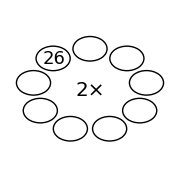

```mathematica
Graphics[c[9,2,26],PlotRange->{-6,6},ImageSize->{180,180}]
```

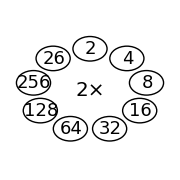

```mathematica
Graphics[d[9,2,{32,16,8,4,2,26,256,128,64}],PlotRange->{-6,6},ImageSize->{180,180}]
```

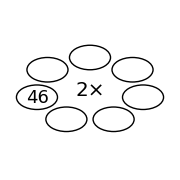

```mathematica
Graphics[c[7,2,46],PlotRange->{-6,6},ImageSize->{180,180}]
```

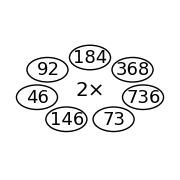

```mathematica
Graphics[d[7,2,{73,736,368,184,92,46,146}],PlotRange->{-6,6},ImageSize->{180,180}]
```

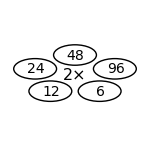

```mathematica
Graphics[d[5,2,{6,96,48,24,12}],PlotRange->{-6,6},ImageSize->{150,150}]
```

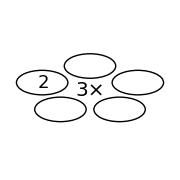

```mathematica
Graphics[c[5,3,2],PlotRange->{-6,6},ImageSize->{180,180}]
```

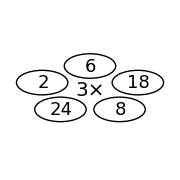

```mathematica
Graphics[d[5,3,{8,18,6,2,24}],PlotRange->{-6,6},ImageSize->{180,180}]
```

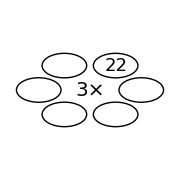

```mathematica
Graphics[c[6,3,22],PlotRange->{-6,6},ImageSize->{180,180}]
```

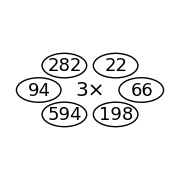

```mathematica
Graphics[d[6,3,{198,66,22,282,94,594}],PlotRange->{-6,6},ImageSize->{180,180}]
```

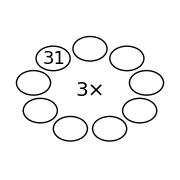

```mathematica
Graphics[c[9,3,31],PlotRange->{-6,6},ImageSize->{180,180}]
```

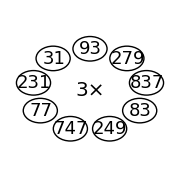

```mathematica
Graphics[d[9,3,{249,83,837,279,93,31,231,77,747}],PlotRange->{-6,6},ImageSize->{180,180}]
```

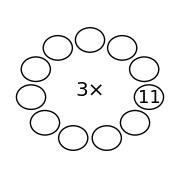

```mathematica
Graphics[c[11,3,11],PlotRange->{-6,6},ImageSize->{180,180}]
```

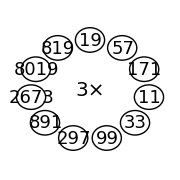

```mathematica
Graphics[d[11,3,{99,33,11,171,57,19,819,8019,2673,891,297}],PlotRange->{-6,6},ImageSize->{180,180}]
```

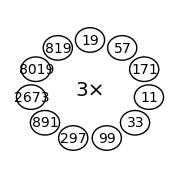

```mathematica
Graphics[d[11,3,{99,33,11,171,57,19,819,8019,2673,891,297}],PlotRange->{-6,6},ImageSize->{180,180}]
```

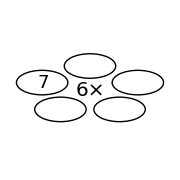

```mathematica
Graphics[c[5,6,7],PlotRange->{-6,6},ImageSize->{180,180}]
```

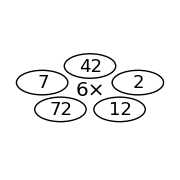

```mathematica
Graphics[d[5,6,{12,2,42,7,72}],PlotRange->{-6,6},ImageSize->{180,180}]
```

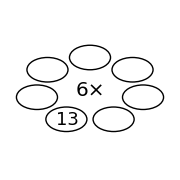

```mathematica
Graphics[c[7,6,13],PlotRange->{-6,6},ImageSize->{180,180}]
```

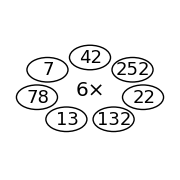

```mathematica
Graphics[d[7,6,{132,22,252,42,7,78,13}],PlotRange->{-6,6},ImageSize->{180,180}]
```

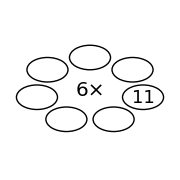

```mathematica
Graphics[c[7,6,11],PlotRange->{-6,6},ImageSize->{180,180}]
```

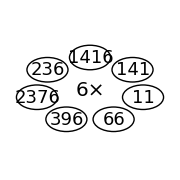

```mathematica
Graphics[d[7,6,{66,11,141,1416,236,2376,396}],PlotRange->{-6,6},ImageSize->{180,180}]
```

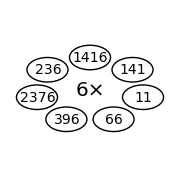

```mathematica
Graphics[dd[7,6,{66,11,141,1416,236,2376,396}],PlotRange->{-6,6},ImageSize->{180,180}]
```

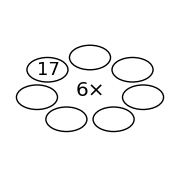

```mathematica
Graphics[c[7,6,17],PlotRange->{-6,6},ImageSize->{180,180}]
```

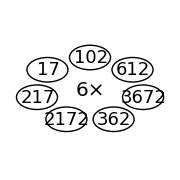

```mathematica
Graphics[d[7,6,{362,3672,612,102,17,217,2172}],PlotRange->{-6,6},ImageSize->{180,180}]
```

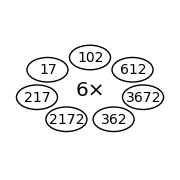

```mathematica
Graphics[dd[7,6,{362,3672,612,102,17,217,2172}],PlotRange->{-6,6},ImageSize->{180,180}]
```

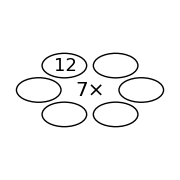

```mathematica
Graphics[c[6,7,12],PlotRange->{-6,6},ImageSize->{180,180}]
```

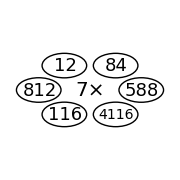

```mathematica
Graphics[d[6,7,{4116,588,84,12,812,116}],PlotRange->{-6,6},ImageSize->{180,180}]
```

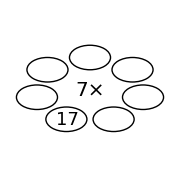

```mathematica
Graphics[c[7,7,17],PlotRange->{-6,6},ImageSize->{180,180}]
```

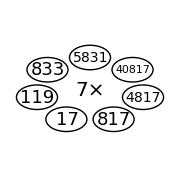

```mathematica
Graphics[d[7,7,{817,4817,40817,5831,833,119,17}],PlotRange->{-6,6},ImageSize->{180,180}]
```

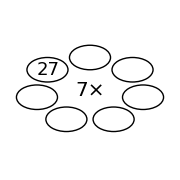

```mathematica
Graphics[c[7,7,27],PlotRange->{-6,6},ImageSize->{180,180}]
```

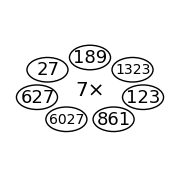

```mathematica
Graphics[d[7,7,{861,123,1323,189,27,627,6027}],PlotRange->{-6,6},ImageSize->{180,180}]
```

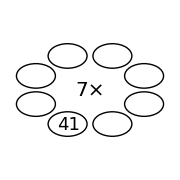

```mathematica
Graphics[c[8,7,41],PlotRange->{-6,6},ImageSize->{180,180}]
```

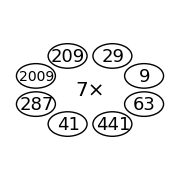

```mathematica
Graphics[d[8,7,{441,63,9,29,209,2009,287,41}],PlotRange->{-6,6},ImageSize->{180,180}]
```